## Data

```mathematica
(* Initialize stuff *)
```

```mathematica
ClearAll["Global`*"];
SetDirectory[NotebookDirectory[]];
Needs["PMC`"];
```

```mathematica
(* Load and extract data *)
```

```mathematica
vrad =SemanticImport["vrad_simu_challenge_0.rdb",ExcludedLines->{2}];
```

```mathematica
data =Normal@vrad[All,#]&/@ {"jdb",(#"rv_planet"+#"rv_osc_and_gran"+#"rv_inst_noise") 1000&,(#"sig_rv"*1000)^2 &};
```

```mathematica
Clear[rvmodel,chi2];
rvmodel[phi_,P_,logK_]:=Module[{f,K=Exp[logK]},
f = 2 Pi (FractionalPart[data[[1]]/P]+phi);
K Cos[f]
]
chi2[phi_?NumericQ,P_?NumericQ,logK_?NumericQ]:=Module[{rv},
rv = rvmodel[phi,P,logK];
Total[(data[[2]]- rv)^2/data[[3]]]
]
```

```mathematica
(* Try a test *)
```

```mathematica
chi2[0.75,16.0,Log[1.5]]
```

2428.85

```mathematica
Clear[plot1,plot2];
plot1[logP_]:=ListPlot[Transpose[{FractionalPart[data[[1]]/Exp[logP]],data[[2]]}]]
plot2[logK_,phi_,st_:Red]:= Plot[Exp[logK]Cos[2 Pi (t + phi)],{t,0,1},PlotStyle->st]
```

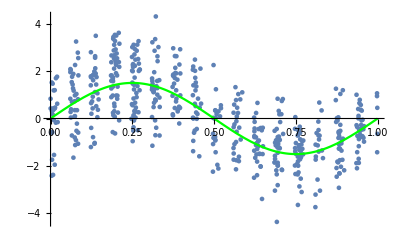

```mathematica
Show[plot1[Log[16]],plot2[Log[1.5],0.75,Green]]
```

## Test case

### The PMC loop

#### Initialize

```mathematica
(* Initialize *)
nd=10;
npop=10000;
mix1 = Table[{1.0,{i/nd,15.55+i/nd,-0.5+i/nd},DiagonalMatrix[{1.0,0.1,0.4}]},{i,0.0,nd-1}];
mix2 = Table[{1.0,{i/nd,24.55+i/nd,-0.5+i/nd},DiagonalMatrix[{1.0,0.1,0.4}]},{i,0.0,nd-1}];
mix = Join[mix1,mix2];
model= buildModels@mix;
eps = DiagonalMatrix[{0.01,0.001,0.01}^2];
Clear[fiddle];
fiddle[x_,y_,z_] := {Mod[x,1],y,z};
fiddle[-0.9,10,10]
```

{0.1,10,10}

#### First look plots

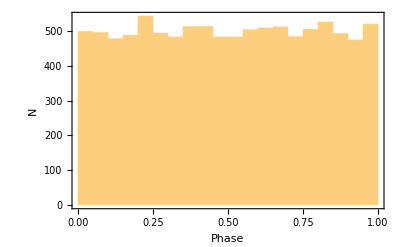

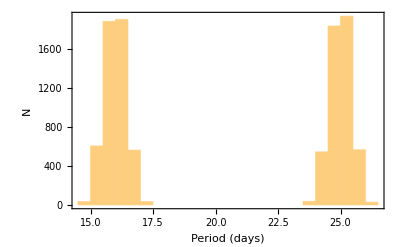

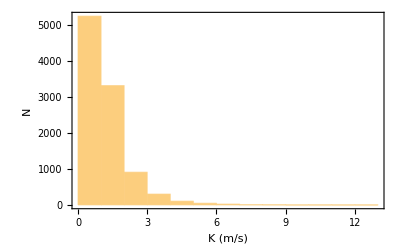

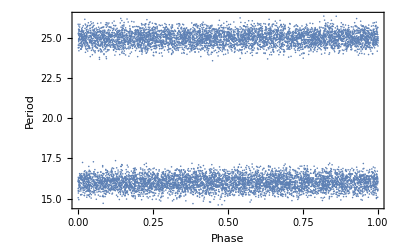

```mathematica
xx = mkRandom[model,npop, fiddle]; (* One off for simplicity *)
Histogram[xx[[All,1]],Frame->True,Axes->False,FrameLabel->{"Phase","N"}]
Histogram[xx[[All,2]],Frame->True,Axes->False,FrameLabel->{"Period (days)","N"}]
Histogram[Exp[xx[[All,3]]],Frame->True,Axes->False,FrameLabel->{"K (m/s)","N"}]
ListPlot[xx[[All,{1,2}]],Frame->True,Axes->False,FrameLabel->{"Phase","Period"}]
```

#### The PMC Loop

```mathematica
(* The PMC loop starts here, execute this cell until the perplexity
gets close to 1 *)
{perplex,xx,model}=iterPMC[chi2,npop,model,eps,fiddle];
perplex
Mean[MixtureDistribution@@model]
StandardDeviation[MixtureDistribution@@model]
```

0.951209

{0.746617,15.9991,0.408458}

{0.00733915,0.00188677,0.0198295}

### Summary plots

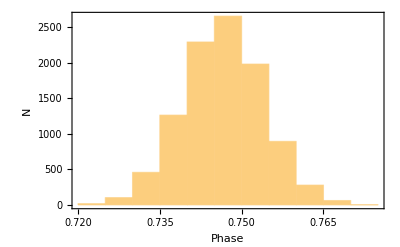

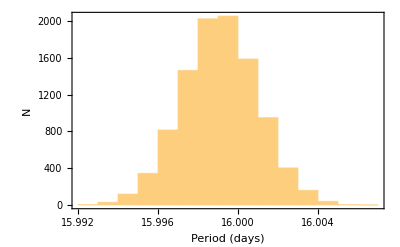

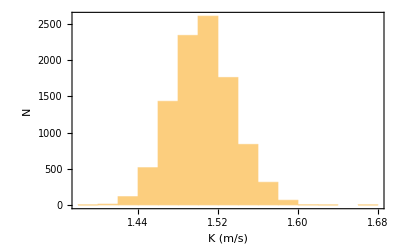

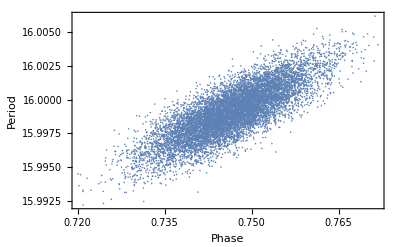

```mathematica
Histogram[xx[[All,1]],Frame->True,Axes->False,FrameLabel->{"Phase","N"}]
Histogram[xx[[All,2]],Frame->True,Axes->False,FrameLabel->{"Period (days)","N"}]
Histogram[Exp[xx[[All,3]]],Frame->True,Axes->False,FrameLabel->{"K (m/s)","N"}]
ListPlot[xx[[All,{1,2}]],Frame->True,Axes->False,FrameLabel->{"Phase","Period"}]
```